```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

```mathematica
n = 10;
Xdata = RandomVariate[NormalDistribution[10,2],{n}];
{α,β} = {0,1};
σ = 1;
Ydata = α+β Xdata + RandomVariate[NormalDistribution[0,σ],{n}];
```

```mathematica
Xdata={10.121344813312856,9.633249288450678,12.27276955920061,11.30355187522552,8.74238937461205,10.034754277128892,10.545613652291843,7.85896347953396,7.80685977134398,9.476746583639176};
Ydata={9.7008064934618,9.931974466098017,12.940646755279321,10.37440336281391,9.22223507614089,11.18748339776299,10.842073636571756,9.938280637577815,8.140378917768192,9.864063572068805};
XNewdata={11.942541359837172,9.418518055280398,5.831716760746266,8.401239275971252,14.615835688820276,7.892479268005209,10.521514016276585,10.366465930332337,9.357969846144147,9.629555586409452};
YNewdata={12.099036564290115,10.334570181546658,7.457972314864254,8.893074596136728,16.067625249797196,9.753353630114326,12.35917838802994,10.603630368963922,8.696296191619933,9.53609179220308};
```

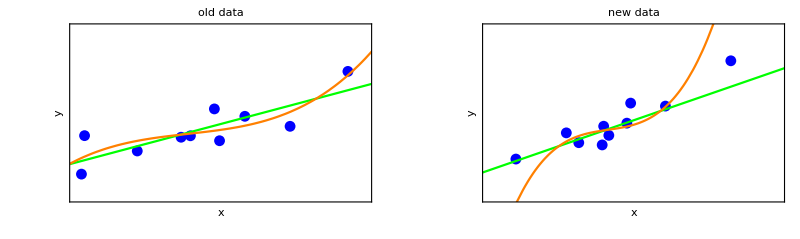

```mathematica
aOverfitModel = LinearModelFit[Thread[{Xdata,Ydata}],{x,x^2,x^3},x];
aBetterModel = LinearModelFit[Thread[{Xdata,Ydata}],x,x];
aTable = Table[aOverfitModel[x],{x,0,Max@Xdata,1}];
gFinal=Show[GraphicsRow[{Show[ListPlot[Thread[{Xdata,Ydata}],Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"x","y"},BaseStyle->{FontSize->16},PlotRange->{{Min@Xdata-0.1,Max@Xdata+0.3},{7,15}},PlotStyle->Blue,PlotLabel->"old data"],Plot[{aBetterModel[x],aOverfitModel[x]},{x,0,20},PlotStyle->{Green,Orange}]],Show[ListPlot[Thread[{XNewdata,YNewdata}],Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"x","y"},PlotLabel->"new data",BaseStyle->{FontSize->16},PlotRange->{{Min@Xdata-0.1-3,Max@Xdata+0.3+4},{7-3,15+4}},PlotStyle->Blue,Axes->False],Plot[{aBetterModel[x],aOverfitModel[x]},{x,0,20},PlotStyle->{Green,Orange}]]}],ImageSize->800]
```

```mathematica
Export["Evaluation_overfit.pdf",gFinal]
```

Evaluation_overfit.pdf